```mathematica
(*Mathematica Notebook Sample of the Larva Continuous Oscillator model system of equations
The Equations are defined and solved to run within a 2d Gaussian used to represent an odour gradient. 

 K. Lagogiannis

This workbook is associated with the eLife article 2016, of Wystrach A., Lagogiannis K., Webb B. 

1st section can 
 *)
```

```mathematica
(*CHEMOTAXIS DEMO 
Change TGain to 40 to lower chemotaxis ability, increase to 80 to get trajectories more concentrated to the centre *)
Clear[A,Xl,Xr,Xcl,Xcr ,s];
ClearAll[g,tauh,hl,cl,hcl];

TGain =80; (*Gain of converting Transient Sensory To Changes stimulus Firing Rate *)

(*Define Odour Gradient*)
rho = 1/5; (*{ρ,{-.7,-0.4,0,0.3,0.5,0.8}}*)
(*s[t_]:= 1000PDF[MultinormalDistribution[{0,0},{{40,rho },{rho,40}}],{x[t],y[t]}];*)
odourGrad:= 1000PDF[MultinormalDistribution[{0,0},{{40,rho },{rho,40}}],{x[t],y[t]}];
Od[xx_,yy_]:=odourGrad/.{x[t]->xx,y[t]->yy};

(*Test the Lamprey  Naka-Rushton version of the oscillators*)
HT =1; (*Set To 0 Gives no NeuronModulation *)
(*Head Mech Model*)
z=1/2;
k=1;


k1 =1/2; (*Feedback Gain of Sensory Neurons *)
bTonus = 19; (*Sensory Tonic Firing Fq*)

(*Run Length Parameters and Extra Exhitatory Stimulus*)
tend = 500;

(*PARAMETER SET - CHEMO1 Works*)
(*Correct Fq With A=15Hz and tauh = 35/...*)
tau = 1/10;
Wce = 1/10;
Wee = 3;
Wec = 4;
Wcc  = Wec;
(*Set Auxiliary equations for Exhitatory Neurons*)
Elin[t] = A[t]+Wee el[t]- Wec cr[t] ;
Erin[t] = A[t]+Wee er[t]- Wec cl[t];

Xl[t]   := Piecewise[{ {Elin[t],(Elin[t])>=0},{0,Elin[t]<0} }];(*Left Exh. Neuron*)
Xr[t]   := Piecewise[{ {Erin[t],Erin[t]>=0},{0,Erin[t]<0} }];

(*Set Auxiliary equations for Inhibitory Neurons*)
Ilin[t] = A[t]+Wce el[t]- Wcc cr[t];
Irin[t] = A[t]+Wce er[t]-Wcc cl[t];

Xcl[t] := Piecewise[{ {Ilin[t],Ilin[t]>=0},{0,Ilin[t]<0} }];
Xcr[t] := Piecewise[{ {Irin[t],Irin[t]>=0},{0,Irin[t]<0} }];

tauh[t_] := 35/(1+(2(A[t])/10)^2); (*Mistake in book this is 0.2+A - A[t] necessary for Checmotaxis*)
g[t_]       :=6+HT(9 (A[t])/100)^2;(*Mistake in book this is 0.09+A - A[t] stimulus not necessary for Chemotaxis*)

(* Do Stim Integ - Here idealized derivative is used s', the use of such equations makes the system differential algebraic, and requires Method->{"IndexReduction"->Automatic} for Mathematica*)
A[t_]        := bTonus + TGain s'[t];


eqnE :={
tau el'[t]== -el[t]+ (100(Xl[t])^2) /( (64 + g[t] hl[t])^2 + (Xl[t])^2),
hl'[t]==1/tauh[t] (-hl[t]+el[t]),
tau cl'[t] == -cl[t] + 100(Xcl[t])^2/((64 + g[t] hcl[t])^2 + (Xcl[t])^2),
hcl'[t] == 1/tauh[t] (-hcl[t]+ el[t]),

tau er'[t]== -er[t]+ (100(Xr[t])^2) /( (64 + g[t] hr[t])^2 + (Xr[t])^2 ),
hr'[t]==1/tauh[t] (-hr[t]+er[t]),
tau cr'[t] == -cr[t] + 100(Xcr[t])^2/((64 + g[t] hcr[t])^2 + (Xcr[t])^2),
hcr'[t] == 1/tauh[t] (-hcl[t]+ er[t]),
 
(*Reorientation dynamics due to Head & Muscle and motion reconstitution - Scaled down rate by 10*)
th''[t] ==-z th'[t] -k (th[t])+(el[t]-er[t]),
brg'[t] == th[t]/10,
x'[t] ==Sin[brg[t]]/10 ,
y'[t] ==Cos[brg[t]]/10 ,
s[t]==Od[x[t],y[t]],

(*Set Start Position Here*)
x[t/;t≤0]==5,y[t/;t≤0]==-5,
el[t/;t≤0]==80,
hl[t/;t≤0]==0,
cl[t/;t≤0]==0,
hcl[t/;t≤0] == 0,
er[t/;t≤0]==20,
hr[t/;t≤0]==0,
cr[t/;t≤0]==0,
hcr[t/;t≤0] == 0,
th[t/;t≤0]==0,
s[t/;t≤0] ==Od[x[0],y[0]],
s'[t/;t≤0] ==0,
(*A'[t/;t≤0]==0,A[t/;t≤0]==bTonus,m[t/;t≤0] == m0,*)
brg[t/;t≤0] == 0
};


(*Run Numerical Solver {"IndexReduction"->Automatic} "EquationSimplification"->"Residual" "ExplicitRungeKutta"*)
sol = NDSolve[eqnE,{el,er,brg,th,x,y,s},{t,0,tend},Method->{"IndexReduction"->Automatic}, MaxSteps->1000000,PrecisionGoal->50, AccuracyGoal->10];
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

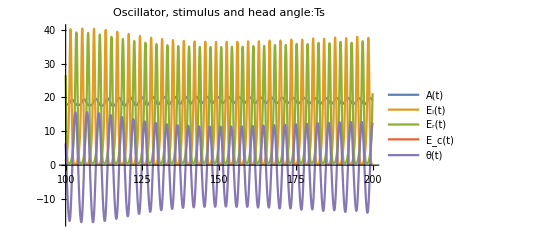

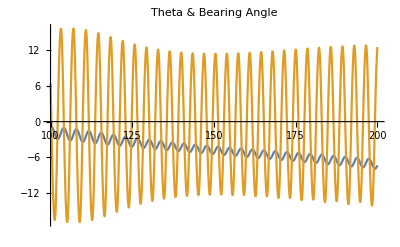

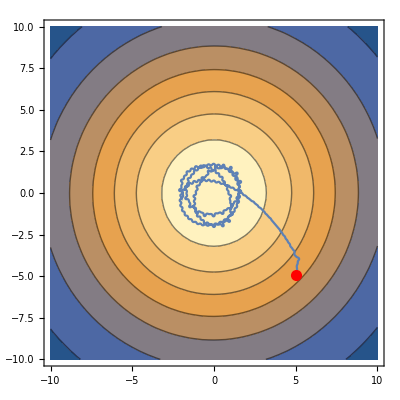

```mathematica
(*CHeck Chemotax Steering*)
(*Plot Responses*)
tinit = 0;
tspot =5;
tinit = 100;
tpend = 200;

Plot[Evaluate[{A[t],el[t],er[t],ec[t],th[t]}/.sol],{t,tinit,tpend},PlotPoints->500,PlotRange->{{tinit,tpend},Full},PlotLabel->"Oscillator, stimulus and head angle:"<>ToString[Ts],PlotLegends->LineLegend[{"A(t)","E_l(t)","E_r(t)","E_c(t)","θ(t)"},LegendLayout->"Column"],Epilog->{Red,PointSize[0.02],Point[{tspot,th[tspot]}/.sol]}]

Plot[Evaluate[ {brg[t],th[t]}/.sol],{t,tinit,tpend},PlotLabel->"Theta & Bearing Angle"]

plotPath = ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tend},PlotLabel->"Chemotax",PlotRange->{{-10,10},{-10,10}},Epilog->{Red,PointSize[0.02],Point[{x[1],y[1]}/.sol]}];

plotOd = ContourPlot[{Od[x,y]},{x,-10,10},{y,-10,10},PlotRange->{{-10,10},{-10,10}},Epilog->{Red,PointSize[0.02],Point[{x[1],y[1]}/.sol]}];

pltChemotax = Show[{plotOd,plotPath}]
```

```mathematica
(* The following code generetes The figure of bearing to odour change Vs stimulus phase. The module measurePertubationEffects
is called repeatedly within a loop that can found after the module code (Bottom of note book). Once run, it saves the output variables to .dat files, but it also plots them in the subdidirectories :
PertubationResults/UnitStep
Sample waveforms of stimulus and oscillator activity  is saved in :
PertubationResults/SampleOscPertubations

*Additionally, to bearing changes, the module also  measures the effects on phase and amplitude on the oscillator when pertubed by a step amplitude sA.

Zero phase is on Peak of L burst found after 100sec init. Stimulations start from -phi located on preceding R burst and go up to the next R burst. Relative Amplitude is of the L burst, and phase is between Mid L burst and L burst preceding last R burst
Added phase mark of begining of Half Max and End of Half Max Burst of Unpertubed System

Parts of the code have been commented out, if activated we can:
*Convert to Pulses (with a fixed duration )  instead of steps 
*Add Periodic Exhitatory Stimulus ExStim, every 1 sec - To simulate effect of propagating perilstatic wave
*Added HTMod - Set to 1 for Neuromodulatory Effects to exist - 0 To Switch Off (Steering goes down significantly, chemotaxis abolished)   *)

measurePertubationEffects[sA_,backA_,HTMod_,steps_] :=
Module[{A,
lstStimPhase= {},lstPeriodL    ={},
lstDPhaseL    ={},lstDPhaseR    ={},
lstDAmpL0       = {},lstDAmpL1       = {},
lstDAmpR1       ={},lstRes = {},sol,Ts=151,phaseMark,tend=160,tinit=100,Dt=1/10,nDt,
ArepEx  (*Amplitude Repetitive Stimulus Pulse every sec*)
}
,
ArepEx = 0;
nDt = (tend-tinit)/Dt; (*Number of sample steps*)

(*Exhitatory Stimulus Pulse of Duration T, with t Setting the onset time t*) 
(*St[tOn_,T_] = UnitStep[(T/2)^2-(tOn-(T/2))^2]; *)
St[tOn_,T_] = UnitStep[tOn]; 
repStimGrid = Flatten[Range[0,tend,1]];
ExStim[t_]= Total[St[t-repStimGrid,1/10]];

A := backA + sA St[t-Ts,1/Sqrt[2]] /; ArepEx == 0;
A:= backA + sA St[t-Ts,1/Sqrt[2]]+ ArepEx ExStim[Ts]/; ArepEx > 0;

(*Neuromodulation*)
g:=6+(9 backA/100)^2 /;HTMod ==0; (*Mistake in book this is 0.09+A*)
tauh := 35/(1+(2backA/10)^2) /;HTMod ==0; (*Mistake in book this is 0.2+A*)

g:=6+(9  A/100)^2 /;HTMod >0; (*Mistake in book this is 0.09+A*)
tauh := 35/(1+(2A/10)^2) /;HTMod >0; (*Mistake in book this is 0.2+A*)

(*Set For Wider Bursts PeakB=60Hz*)
tau = 1/10; Wec = 1/10; Wc = 6;  Wee = 4;
(*Correct Fq With A=15Hz and tauh = 35/...*)
tau = 1/10;Wec = 1/10;Wc = 10; Wee = 3;

(*Set Used for Chemotax Results - with Fq Correct*)
tau = 1/10;Wc = 4;Wec = 1/10;Wee = 3;
 Wce = 0/25;(*Ipsilateral Connection - Set To Zero To Remove*)

(*Head Mech Model*)
zeta=1/2; (*Damping Ratio 2zeta = z/Sqrt(m k)*)

(*Xl[t_] := Piecewise[{ {A+6e[t]-c[t],(A+6e[t]-c[t])>=0},{0,A+6e[t]-c[t]>0} }]*)
Xl[t]   := Piecewise[{ {A+Wee el[t]- Wc cr[t],(A+Wee el[t]- Wc cr[t])>=0},{0,(A+Wee el[t]- Wc cr[t])<0} }];
Xr[t]   := Piecewise[{ {A+Wee er[t]- Wc cl[t],(A+Wee er[t]-Wc cl[t])>=0},{0,(A+Wee er[t]- Wc cl[t])<0} }];
Xcl[t] := Piecewise[{ {A+Wec el[t]- Wc cr[t],(A+Wec el[t]-Wc cr[t])>=0},{0,(A+Wec el[t]-Wc cr[t])<0} }];
Xcr[t] := Piecewise[{ {A+Wec er[t]-Wc cl[t],(A+Wec er[t]-Wc cl[t])>=0},{0,(A+Wec er[t]- Wc cl[t])<0} }];
eqnE :={
tau el'[t]== -el[t]+ (100(Xl[t])^2) /( (64 + g hl[t])^2 + (Xl[t])^2),
hl'[t]==1/tauh (-hl[t]+el[t]),
tau cl'[t] == -cl[t] + 100(Xcl[t])^2/((64 + g hcl[t])^2 + (Xcl[t])^2),
hcl'[t] == 1/tauh (-hcl[t]+ el[t]),
tau er'[t]== -er[t]+ (100(Xr[t])^2) /( (64 + g hr[t])^2 + (Xr[t])^2 ),
hr'[t]==1/tauh (-hr[t]+er[t]),
tau cr'[t] == -cr[t] + 100(Xcr[t])^2/((64 + g hcr[t])^2 + (Xcr[t])^2),
hcr'[t] == 1/tauh (-hcl[t]+ er[t]),
(*Head & Muscle Model*)
 th''[t] ==- 2zeta th'[t] - (th[t])+(el[t]-er[t]),
brg'[t] == th[t]/10,

el[0]==1,hl[0]==0,cl[0]==0,hcl[0] == 0,er[0]==0,hr[0]==0,cr[0]==0,hcr[0] == 0,brg[0]==0,th[0]==0,th'[0]==0}; 

(*Make Empty Lists of - Change of Amplitude - Change IN Period - Change in Phase - and Phase of stimulus delivery*)

TpkLAfterStim = 0;

(*Measure Phase Response Model - Burst Duration - fq - Amplitude*)
Steps = steps;
grid=Range[tinit,tinit+(nDt-1)*Dt,Dt];
Monitor[
For[ i=0,i≤(Steps+1),i++,

sol = NDSolve[eqnE,{el,er,th,brg},{t,tend},Method->Automatic,MaxSteps->100000];

lstEl = Table[Flatten[{i,el[i]/.sol}],{i,tinit-5,115,Dt}];
(*lstEl = Flatten[el[grid]/.sol];*)
Elpks =FindPeaks[lstEl[[All,2]],0,Automatic,3];
Elpks = lstEl[[Elpks[[All,1]]]];

lstEr = Table[Flatten[{i,er[i]/.sol}],{i,tinit-5,115,Dt}];
(*lstEr = Flatten[er[grid]/.sol];*)
Erpks =FindPeaks[lstEr[[All,2]],0,Automatic,3];
Erpks = lstEr[[Erpks[[All,1]]]];


(*INIT VARS - OF UNPERTURBED SYSTEM Locate A peak point to Start The Stimulus*)
If[i==0,
(* Since Ts = 150 - 95 is Choose A point of 1st stim, at some point when the limit cycle is stable - This will also be the Zero Phase Mark 
- On Step 0, there is no stimulus before 95-*)
(*Take the first R peak found After 100 sec and set as the initial stimulus time Ts*)
Ts = Extract[Take[Select[Erpks[[All,1]],#>tinit &],1],1];

(*Find Two L peak times prior to Ts*)
TpkLPriorToStim = Take[Select[Elpks[[All,1]],#≤(Ts) &],-2];
(*Find a L peak times after to Ts*)
TpkLAfterStim     = Take[Select[Elpks[[All,1]],# >=(Ts) &],1];
(*Find Two R peak times prior to Ts*)
TpkRPriorToStim = Take[Select[Erpks[[All,1]],#≤(Ts) &],-2];
(*Find a R peak times after to Ts*)
TpkRAfterStim     = Take[Select[Erpks[[All,1]],#>Ts &],1];

(*Take Mean amplitude for each L and R given n=1, starting from the 2nd peak prior to stimulus*)
meanAmpEl = Mean[Take[Select[Elpks,#[[1]]<TpkLPriorToStim[[2]] &][[All,2]],-1]];
meanAmpEr = Mean[Take[Select[Erpks,#[[1]]<TpkRPriorToStim[[2]] &][[All,2]],-1]];
PrintTemporary["Mean Ampl L:"<>ToString[meanAmpEl] ];

(*Set Zero Phase Mark To the peak Before Stim of the R Oscillator*)
Tzpm = TpkRPriorToStim[[2]];
(*1st Stim At Zero point Marker - On R Peak*)
Ts = Tzpm;
(*However Zero Phase Mark for phaseMark Measurements is the peak of the L burst*)
TzpmL = Extract[TpkLAfterStim,1];
TPeriodFullNorm =Tzpm-TpkRPriorToStim[[1]] ;
(*Get Time of EL-To-ER burst - On this point there is no stimulus so measured period acts as a control*)
TPeriodOppositeNorm =Tzpm - TpkLPriorToStim[[2]];

(*FIND time Start Of Half-Max L Burst - And End time point*)
BurstHWidthL = Select[ lstEl,#[[1]]>(Tzpm)  && #[[1]]<(Extract[TpkRAfterStim,1]) && #[[2]]>meanAmpEl/2 &];
TBurstLInit   = First[BurstHWidthL[[All,1]]];
TBurstLEnd     =Last[BurstHWidthL[[All,1]]];

(*Get Baseline Bearing Once the system has settled*)
BrgInit =  Extract[Flatten[NIntegrate[{brg[t]/(tend-Ts)}/.sol,{t,Ts,tend}]],1];

phaseBInitMark = (TBurstLInit- TzpmL)/TPeriodFullNorm;
phaseBEndMark = (TBurstLEnd- TzpmL)/TPeriodFullNorm;


Print["**New Run with stim Time:"<>ToString[N[Ts,2]]];
Print["Z.Phase t:"<>ToString[N[Tzpm,2]] <> " Period :"<>ToString[N[TPeriodFullNorm,2]] <> " Fq:" <> ToString[N[1/TPeriodFullNorm,2]] <> " H.Period :"<>ToString[N[TPeriodOppositeNorm,2]] <> " Brst Wdth:" <> ToString[N[TBurstLEnd-TBurstLInit,2]] ];


phaseMark = (Ts - TzpmL)/TPeriodFullNorm;
(*Plot A sample Oscillation and Stimuli*)

pltOsc = Plot[Evaluate[{{el[t],er[t],th[t],th'[t]}/.sol,A}],{t,Tzpm,Tzpm+TPeriodFullNorm},PlotPoints->1500,Frame->True,FrameLabel->{"Time","Firing rate (Hz)/Angle"},PlotLegends->Placed[LineLegend[{"L Oscillator","R Oscillator","Head Θ","Head Θ'","Input @
StyleBox[\"Φ\",\nFontSize->14]:"<> ToString[N[phaseMark,3]]}],{0.5,0.8}], PlotRange->{{Tzpm,Tzpm+TPeriodFullNorm},{-20,100}},PlotLabel->"Bursting Coupled Oscillators L-R",Epilog->{{Red,PointSize[0.02],Point[Join[Elpks,Erpks]]},{Blue,PointSize[0.01],Point[BurstHWidthL]}}];

SetDirectory[NotebookDirectory[]];
Export["PertubationResults/SampleOscPertubations/OscillationsUnitStep"<>ToString[i]<>"_A"<>ToString[backA]<>"S"<>ToString[sA]<>"E"<>ToString[ArepEx]<>"HT"<> ToString[HTMod]<>".pdf",pltOsc];

(*Skip To next Loop cycle*)
Continue[];
 

]; (*End 1st Cycle Only Calculations on Unperturbed system*)


(*Time of 1st peak after Zero Phase Mark - I use <Ts for the peak on the Zpm*)
(*Stick to period around Tzpm for 1st peak* - add a margin as 1st peak shift on stim*)
TpkLPriorToStim = Extract[Take[Select[Elpks[[All,1]],#≤(Tzpm) &],-1],1];
TpkLAfterStim = Extract[Take[Select[Elpks[[All,1]],#>(Tzpm) &],1],1];
(*Use time of 1st L peak (peak found before end of stim (should be Tzpm))*)
TpkRAfterStim = Extract[Take[Select[Erpks[[All,1]],#>=(Tzpm) &],1],1];

AmpLAfterStim = Extract[el[TpkLAfterStim ]/.sol,1];
AmpRAfterStim =  Extract[er[TpkRAfterStim]/.sol,1];


(*Change In Phase After Stim TpkLPriorToStim*)
DTPeriodStim = TpkLAfterStim-TpkLPriorToStim;
DTPeriodRStim = TpkRAfterStim-TpkLPriorToStim ;

(*Change in Amplitude After Stim*)
DAmpL1 =AmpLAfterStim/ meanAmpEl;
DAmpR1 =AmpRAfterStim/ meanAmpEr;

(*Burst Length*)
(*FIND time Start Of Half-Max L Burst - And End time point*)
BurstHWidthL = Select[lstEl,#[[1]]>(TpkLAfterStim-TPeriodOppositeNorm)  && #[[1]]<(TpkLAfterStim+TPeriodOppositeNorm) && #[[2]]>AmpLAfterStim/2 &];

(*Catch Strange Situation And Plot Error*)
If[Length[BurstHWidthL[[All,1]]] > 0,
DBurstWidthL  = ( Last[ BurstHWidthL[[All,1]] ]-First[ BurstHWidthL[[All,1]]  ])/(TBurstLEnd-TBurstLInit);
,
(*Plot A sample Oscillation and Stimu*)
pltBurstWProb= Plot[Evaluate[{{el[t],er[t],th[t]}/.sol,A}],{t,95,115},PlotPoints->1500,Frame->True,FrameLabel->{"Time","Firing rate/Hz"},PlotLegends->Placed[LineLegend[{"L Oscillator","R Oscillator","Input stimulus @
StyleBox[\"Φ\",\nFontSize->14]:"<> ToString[N[phaseMark,3]]}],{0.7,0.8}], PlotRange->{Full,{0,100}},PlotLabel->"Bursting Coupled Oscillators L-R",Epilog->{{Red,PointSize[0.02],Point[Join[Elpks,Erpks]]},{Blue,PointSize[0.01],Point[BurstHWidthL]}}];

DBurstWidthL = 0;
Show[pltBurstWProb]

];

(*Show Normal Oscillation - Plot the Response Close to Half Way between phase i.e on the peak of the L  *)
If[i== (Round[steps/2]+1),
(*Plot A sample Oscillation and Stimu*)
pltOsc = Plot[Evaluate[{{el[t],er[t],th[t]}/.sol,A}],{t,tinit,tinit+2TPeriodFullNorm},PlotPoints->1500,Frame->True,FrameLabel->{"Time","Firing rate (Hz)/Angle"},PlotLegends->Placed[LineLegend[{"L Oscillator","R Oscillator","Head Θ","Input @
StyleBox[\"Φ\",\nFontSize->14]:"<> ToString[N[phaseMark,3]]}],{0.5,0.8}], PlotRange->{{tinit,tinit+2TPeriodFullNorm},{-20,100}},PlotLabel->"Bursting Coupled Oscillators L-R",Epilog->{{Red,PointSize[0.02],Point[Join[Elpks,Erpks]]},{Blue,PointSize[0.01],Point[BurstHWidthL]}}];
(*Show[pltOsc]*)
SetDirectory[NotebookDirectory[]];
Export["PertubationResults/SampleOscPertubations/OscillationsStep"<>ToString[i]<>"_A"<>ToString[backA]<>"S"<>ToString[sA]<>"E"<>ToString[ArepEx]<>"HT"<> ToString[HTMod]<>".pdf",pltOsc];

 ];


(*Bearing Change Once the system has settled*)
DBrg =  Extract[Flatten[NIntegrate[{brg[t]/(tend-Ts)}/.sol,{t,Ts,tend}]],1]-BrgInit;

(*Append Results to List*)
lstStimPhase   =  Append[lstStimPhase,Ts];

phaseMark = (Ts - TzpmL)/TPeriodFullNorm;
 
(*Result Vector Contains, phaseMark of stimulation, Phase Change, Amplitude change*)
lstRes = Append[lstRes,Flatten[{phaseMark,DTPeriodStim/TPeriodFullNorm,DAmpL1,DBurstWidthL,DBrg/Degree},1 ]  ];
(*Update Next Stimulus Time*)
Ts = Ts+ TPeriodFullNorm/Steps;
(*PrintTemporary[ "Phi: "<> ToString[phaseMark] <> " T till Rpeak:" <> ToString[DTPeriodRStim] <> " Dbearing:" <> ToString[DBrg/Degree] ]; 
PrintTemporary["Peak A:" <> ToString[AmpLAfterStim]];
PrintTemporary["Burst Width:" <> ToString[DBurstWidthL]];*)


]; (*End FOR LOOP*)
,i]; (*End MONITOR*)
(*Save Results*)

pertRes = lstRes;
Save["PertubationResults/PRCUnitStep-BRG-A"<>ToString[backA]<>"S"<>ToString[sA]<>"E"<>ToString[ArepEx]<>"HT"<> ToString[HTMod]<>"Steps"<> ToString[steps]<>".dat",{pertRes,phaseBInitMark,phaseBEndMark}];

Return[lstRes];
];(*END MODULE*)
```

Calc. Effects of +/- Perturbation Size:2

**New Run with stim Time:      2
1.0 10

Z.Phase t:      2
1.0 10 Period :3.6 Fq:0.28 H.Period :1.8 Brst Wdth:0.70

**New Run with stim Time:      2
1.0 10

Z.Phase t:      2
1.0 10 Period :3.6 Fq:0.28 H.Period :1.8 Brst Wdth:0.70

Calc. Effects of +/- Perturbation Size:3

**New Run with stim Time:      2
1.0 10

Z.Phase t:      2
1.0 10 Period :3.6 Fq:0.28 H.Period :1.8 Brst Wdth:0.70

**New Run with stim Time:      2
1.0 10

Z.Phase t:      2
1.0 10 Period :3.6 Fq:0.28 H.Period :1.8 Brst Wdth:0.70

Calc. Effects of +/- Perturbation Size:4

**New Run with stim Time:      2
1.0 10

Z.Phase t:      2
1.0 10 Period :3.6 Fq:0.28 H.Period :1.8 Brst Wdth:0.70

**New Run with stim Time:      2
1.0 10

Z.Phase t:      2
1.0 10 Period :3.6 Fq:0.28 H.Period :1.8 Brst Wdth:0.70

Calc. Effects of +/- Perturbation Size:5

**New Run with stim Time:      2
1.0 10

Z.Phase t:      2
1.0 10 Period :3.6 Fq:0.28 H.Period :1.8 Brst Wdth:0.70

**New Run with stim Time:      2
1.0 10

Z.Phase t:      2
1.0 10 Period :3.6 Fq:0.28 H.Period :1.8 Brst Wdth:0.70

Calc. Effects of +/- Perturbation Size:6

**New Run with stim Time:      2
1.0 10

Z.Phase t:      2
1.0 10 Period :3.6 Fq:0.28 H.Period :1.8 Brst Wdth:0.70

**New Run with stim Time:      2
1.0 10

Z.Phase t:      2
1.0 10 Period :3.6 Fq:0.28 H.Period :1.8 Brst Wdth:0.70

Calc. Effects of +/- Perturbation Size:7

**New Run with stim Time:      2
1.0 10

Z.Phase t:      2
1.0 10 Period :3.6 Fq:0.28 H.Period :1.8 Brst Wdth:0.70

**New Run with stim Time:      2
1.0 10

Z.Phase t:      2
1.0 10 Period :3.6 Fq:0.28 H.Period :1.8 Brst Wdth:0.70

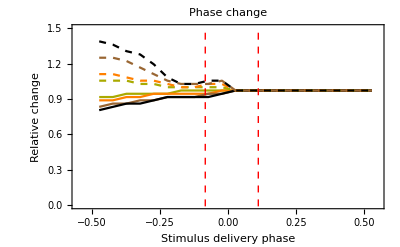

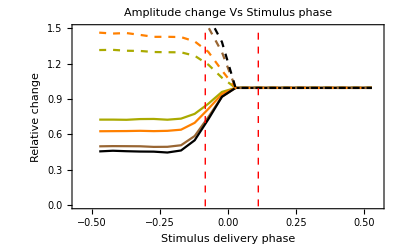

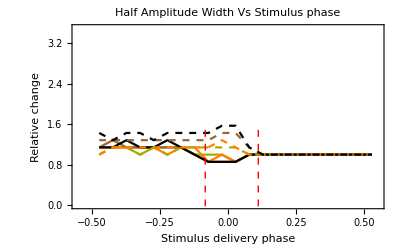

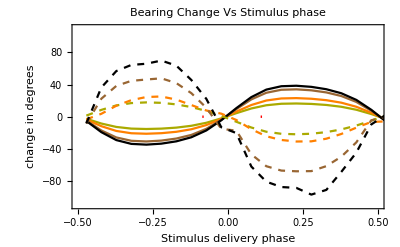

PertubationResults/UnitStep/AmplitudeVsStimPhaseE0HT1.pdf

PertubationResults/UnitStep/PhaseVsStimPhaseE0HT1.pdf

PertubationResults/UnitStep/BurstWidthVsStimPhaseE0HT1.pdf

PertubationResults/UnitStep/BearingChangeVsStimPhaseE0HT1.pdf

```mathematica
(*OBTAIN RESULTS - Iterate through Up/Down StepSizes*)
(*Calculate Phase and Amplitude PRC for 3 Amplitude Strengths*)

startStim = 2;
bgTonus = 19;
HT = 1;
steps = 20;

pertUp = {};
pertDwn = {};

For [Amp = startStim,Amp < 8,Amp++,
Print["Calc. Effects of +/- Perturbation Size:" <> ToString[Amp]];
pertUp =Append[pertUp, measurePertubationEffects[Amp,bgTonus,HT,steps] ];
pertDwn=Append[pertDwn,  measurePertubationEffects[-Amp,bgTonus,HT,steps] ];
startStim = Amp;
(*Save Partial Results - Cummulatively*)
SetDirectory[NotebookDirectory[]];
filename = "PertubationResults/PRCUnitStep-BRG-SAll-A"<>ToString[bgTonus]<>"E0HT"<> ToString[HT]<>".dat";
Save[filename,{pertUp,pertDwn ,startStim,phaseBInitMark,phaseBEndMark,HT,bgTonus}];
];



(*Load Pertubation Results From File
SetDirectory[NotebookDirectory[]];
<<"PertubationResults/PRC-BRG-SALL-A19E0HT1.dat"*)


(*Generate Plot Results - and Export PDFs*)
lgndLin ={"+1","+2","+4","+5","-1","-2","-4","-5"};
ps ={{Normal,Darker[Yellow]},{Normal,Orange},{Normal,Brown},{Normal,Black},{Dashed,Darker[Yellow]},{Dashed,Orange},{Dashed,Brown},{Dashed,Black}};
table[pairs_]:=TableForm[pairs,TableAlignments->Left,TableSpacing->{2,1},TableDirections->Row];
grd[pairs_]:=GraphicsGrid[pairs,Frame->All];

lineBurstInit=Line[{{phaseBInitMark,-1.5},{phaseBInitMark,1.5}}];
lineBurstEnd=Line[{{phaseBEndMark,-1.5},{phaseBEndMark,1.5}}];

pltPhase =ListPlot[Join[Table[pertUp[[a,All,{1,2}]],{a,{1,2,4,5}}],Table[pertDwn[[a,All,{1,2}]],{a,{1,2,4,5}}]],PlotRange->{{-0.55,0.55},{0,1.5}},Joined->True,Frame->True,PlotLabel->"Phase change",PlotLegends->Placed[ 
LineLegend[ lgndLin,LegendLayout->table,LegendLayout->"Row" ],{0.5,0.2} ],
FrameLabel->{"Stimulus delivery phase","Relative change"},PlotStyle->ps,Epilog->{Red,Dashed,lineBurstInit,lineBurstEnd}];

pltAmp = ListPlot[Join[Table[pertUp[[a,All,{1,3}]],{a,{1,2,4,5}}],Table[pertDwn[[a,All,{1,3}]],{a,{1,2,4,5}}]],Joined->True,Frame->True,FrameLabel->{"Stimulus delivery phase","Relative change"}, PlotRange->{{-0.55,0.55},{0,1.5}},PlotLabel->"Amplitude change Vs Stimulus phase",PlotLegends->Placed[ 
LineLegend[ lgndLin,LegendLayout->table,LegendLayout->"Row" ],{0.5,0.2} ],PlotStyle->ps,Epilog->{Red,Dashed,lineBurstInit,lineBurstEnd}];

pltBurstWidth = ListPlot[Join[Table[pertUp[[a,All,{1,4}]],{a,{1,2,4,5}}],Table[pertDwn[[a,All,{1,4}]],{a,{1,2,4,5}}]],Joined->True,Frame->True,FrameLabel->{"Stimulus delivery phase","Relative change"}, PlotRange->{{-0.55,0.55},{0,3.5}},PlotLabel->"Half Amplitude Width Vs Stimulus phase",PlotLegends->Placed[ 
LineLegend[ lgndLin,LegendLayout->table,LegendLayout->"Row" ],{0.5,0.2} ],PlotStyle->ps,Epilog->{Red,Dashed,lineBurstInit,lineBurstEnd}];

pltBearingChange = ListPlot[Join[Table[pertUp[[a,All,{1,5}]],{a,{1,2,4,5}}],Table[pertDwn[[a,All,{1,5}]],{a,{1,2,4,5}}]],Joined->True,Frame->True,FrameLabel->{"Stimulus delivery phase","change in degrees"}, PlotRange->{{-0.50,0.50},{-110,110}},PlotLabel->"Bearing Change Vs Stimulus phase",PlotLegends->Placed[ 
LineLegend[ lgndLin,LegendLayout->table ],{0.5,0.1} ],PlotStyle->ps,Epilog->{Red,Dashed,lineBurstInit,lineBurstEnd}];

Show[pltPhase]
Show[pltAmp]
Show[pltBurstWidth]
Show[pltBearingChange]


SetDirectory[NotebookDirectory[]];
Export["PertubationResults/UnitStep/AmplitudeVsStimPhaseE0HT"<> ToString[HT]<>".pdf",pltAmp]
Export["PertubationResults/UnitStep/PhaseVsStimPhaseE0HT"<> ToString[HT]<>".pdf",pltPhase]
Export["PertubationResults/UnitStep/BurstWidthVsStimPhaseE0HT"<> ToString[HT]<>".pdf",pltBurstWidth]
Export["PertubationResults/UnitStep/BearingChangeVsStimPhaseE0HT"<> ToString[HT]<>".pdf",pltBearingChange]
```